## Particle in a Potential Well

### The Even Solutions we Found on Friday

We tackled the particle in a potential well, which is the particle in a box problem, except the sides of the box are only V_0 high instead of infinitely high. We focused on the even solutions, and we didn’t bother normalizing them. Although we didn’t bother normalizing the solutions, we used normalizability. We also used continuity. With those things, we found:

For -L/2<x<L/2, with p=ℏk=√(2mE) we found ψ(x)=cos kx.

For x>L/2, with ℏκ=√(2m(V_0-E)) we found ψ(x)=cos kL/2 e^(κL/2)e^-κx.

For x<-L/2, we found ψ(x)=cos kL/2 e^(-κL/2)e^κx.

### The Final Condition, No Kinks

We demanded no kink at x=L/2 and we found κ=ktan kL/2. Putting in what κ and k are turned this into:

√((V_0-E)/E)=tan((√(2mE))/ℏ L/2)

This equation tells us the allowed values of E! But it is a hard equation to solve.

### What Now!?

The above equation is a tough one. Fundamentally, the problem is that there are three energies in the problem: E, V_0, and the energy you can make out of the three constants ℏ, m, and L. If there were only two energies in the problem, then you know by dimensional analysis, that they would have to be proportional to each other, and there would be some constants that you can’t get from dimensional analysis, but which you could assume are going to be reasonable things like π^2, 1/8, ln2, etc.

So let’s do the following. Let’s take the combination h^2/(8m L^2)=(ℏ^2 π^2)/(2m L^2) and measure all other energies in terms of that combination. I used that combination, because it is what showed up in the quanton-in-a-box problem. The tough equation becomes:

√((V_0(ℏ^2 π^2)/(2m L^2)-E(ℏ^2 π^2)/(2m L^2))/(E(ℏ^2 π^2)/(2m L^2)))=tan((√(2mE(ℏ^2 π^2)/(2m L^2)))/ℏ L/2)

which simplifies to

√((V_0 -E)/E)=tan(√E π)/2

Now V_0 and E are pure (meaning dimensionless) numbers! The equation looks a lot simpler, but we still are not done!

### Graphical Solution, Large V_0, Even Solutions

Let’s graph this darned thing for a big value of V_0. Later on we’ll graph it for a small value of V_0, and if we haven’t learned enough then will do an intermediate value of V_0. How about V_0=100. The graph of the LHS is:

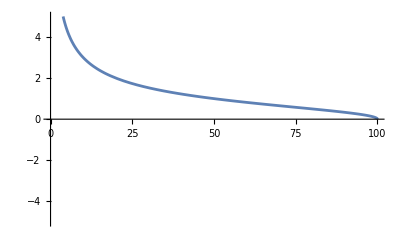

```mathematica
v0=100;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

The graph of the RHS doesn’t depend on V_0. It is:

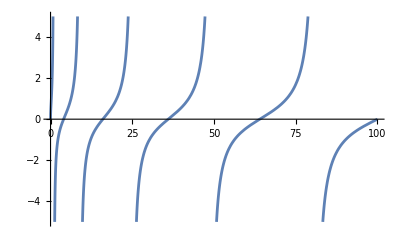

```mathematica
Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

It looks like we will get 5 of these even solutions!

### Graphical Solution, Large V_0, Odd Solutions

If we had done the odd solutions, we would have gotten:

√((V_0-E)/E)=-cot((√(2mE))/ℏ L/2)

The RHS is now:

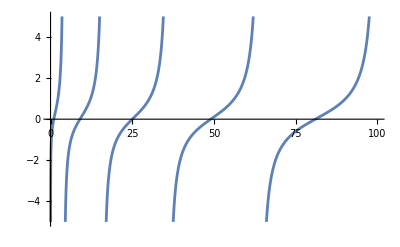

```mathematica
Plot[-Cot[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

It looks like we will get 5 of these odd solutions too! So 10 solutions for V_0=100. Interesting. Maybe you tend to get √V_0solutions?

### Graphical Solution, Really Large V_0, Even Solutions

Let’s just test the idea that you tend to get √V_0solutions. How about we do V_0=10000. We’d expect 100 solutions, 50 of which will be even:

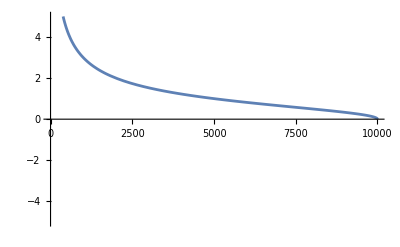

```mathematica
v0=10000;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

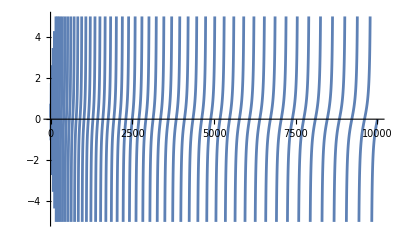

```mathematica
v0=Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

Pretty clearly, there are 50 even solutions, and there will be 50 more odd solutions.

### Graphical Solution, Moderate V_0, Even and Odd Solutions

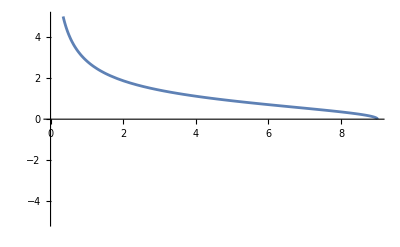

```mathematica
v0=9;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

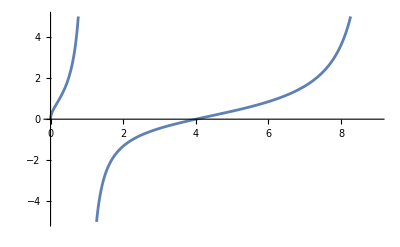

```mathematica
Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

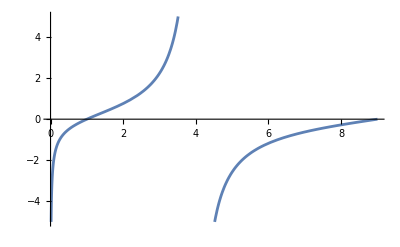

```mathematica
Plot[-Cot[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

Now we have 2 even solutions and 1 odd solution.

### Graphical Solution, Small V_0, Even and Odd Solutions

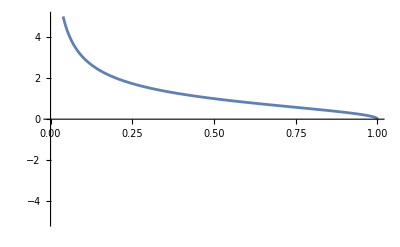

```mathematica
v0=1;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

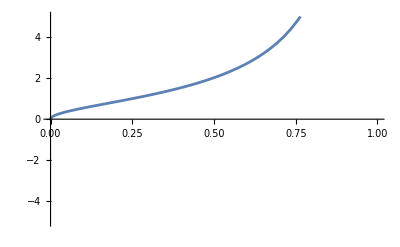

```mathematica
Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

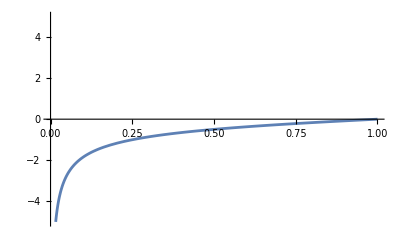

```mathematica
Plot[-Cot[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

We have lost the odd solution, but we still have an even one.

### Graphical Solution, Tiny V_0, One Even Solution Remains

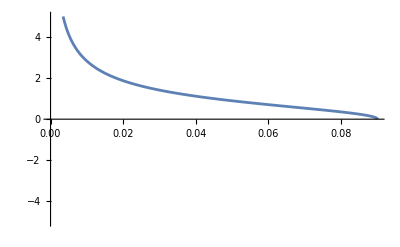

```mathematica
v0=0.09;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

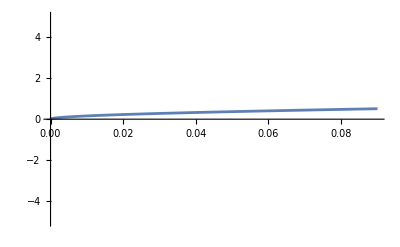

```mathematica
Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

One even solution is still with us!

### Graphical Solution, Really Tiny V_0, One Even Solution Still Remains

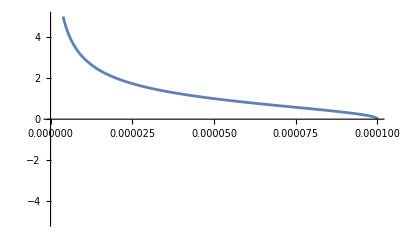

```mathematica
v0=0.0001;Plot[√((v0-energy)/energy),{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

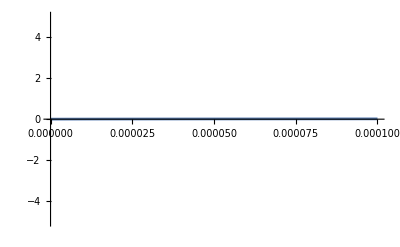

```mathematica
Plot[Tan[(√energy Pi)/2],{energy, 0, v0}, PlotRange->{{0,v0},{-5,5}}]
```

It is clear that no matter how small we make V_0, there is going to be a solution with E just slightly less than V_0.

### The One Solution that Remains for Tiny V_0

It is clear that the one solution that remains for tiny V_0 has E just slightly less than V_0. So in addition to making the approximation that V_0 is small, we can make the approximation that 

E=V_0(1-ϵ)

with epsilon small and positive.

The three equations we want to work on in this approximation are:

√((V_0 -E)/E)=tan(√E π)/2

Let’s find ϵ. The equation above becomes

√((V_0 -V_0(1-ϵ))/(V_0(1-ϵ)))=tan(√(V_0(1-ϵ))π)/2

or

√ϵ=tan(√V_0 π)/2=(√V_0 π)/2

### The Wave Function for Tiny V_0

It sure would be nice to look at the wave function, not just its energy. To get the above equation for the energy, before we even made the approximation, E=V_0(1-ϵ) we had already creatively  measured all energies in units of (ℏ^2 π^2)/(2m L^2).

So let’s do that to the equations for k and κ too.

ℏk=√(2mE(ℏ^2 π^2)/(2m L^2)) and ℏκ=√(2m(V_0(ℏ^2 π^2)/(2m L^2)-E(ℏ^2 π^2)/(2m L^2)))

These now simplify nicely to

k=√E π/L   and   κ=√(V_0 -E)π/L

Let’s be even more creative and measure all lengths in units of L. Then the equations for k and κ which have units of inverse length, further simplify to:

k=√E π   and   κ=√(V_0 -E)π

and the wave function which is a function of x, which has dimensions of length, simplifies to

for -1/2<x<1/2, it is ψ(x)=coskx,

for x>1/2, it is ψ(x)=cos k/2 e^(κ/2)e^-κx,

and for x<-1/2, it is ψ(x)=cos k/2 e^(-κ/2)e^κx.

Using E=V_0(1-ϵ), k and κ approximate to:

k=√(V_0(1-ϵ))π=√V_0 π   and   κ=√(ϵ V_0)π=(√V_0 π √V_0 π)/2=V_0 π^2/2

### Let’s Graph the Wave Function for Tiny V_0

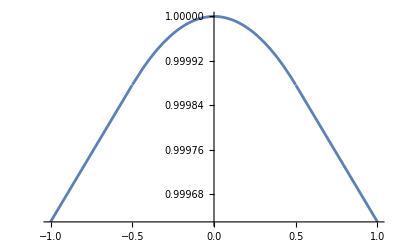

```mathematica
vzero=0.0001;κ=vzero*Pi^2/2; k=Sqrt[vzero]*Pi;
ψ[x_]:=If[Abs[x]>1/2,Cos[k/2]Exp[κ/2]Exp[-κAbs[x]],Cos[kx]];plot[range_]:=Plot[ψ[x],{x, -range, range}];
plot[1]
```

I have zoomed in on the central region to make sure that it is continuous and has no kink at x=±L/2, which is x=±1/2 in our creative units.

Now let’s zoom out.

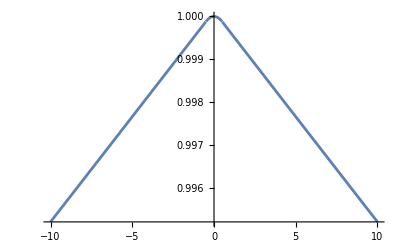

```mathematica
plot[10]
```

Zoom farther out:

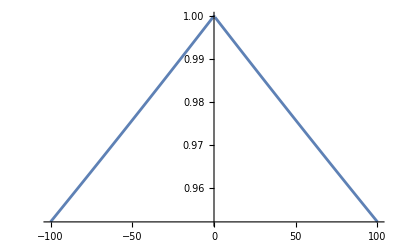

```mathematica
plot[100]
```

Zoom much farther out:

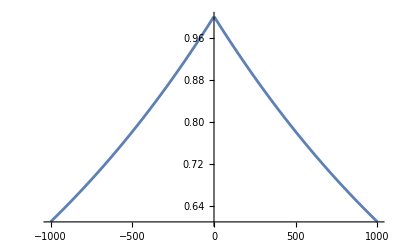

```mathematica
plot[1000]
```

Zoom way the heck out:

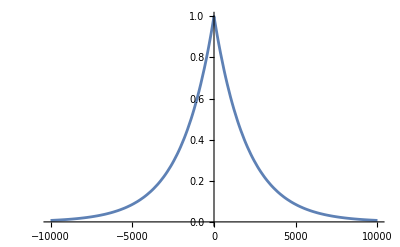

```mathematica
plot[10000]
```

### Normalized Probability Distribution

If you want to normalize the wave function and then square it, it is:

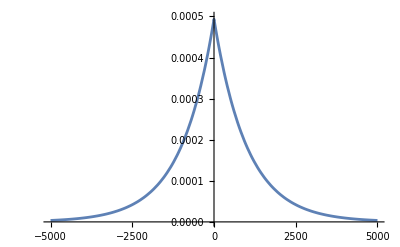

```mathematica
vzero=0.0001;κ=vzero*Pi^2/2; k=Sqrt[vzero]*Pi;
psinormalized[x_]:=Sqrt[κ]If[Abs[x]>1/2,Cos[k/2]Exp[κ/2]Exp[-κAbs[x]],Cos[kx]];
plot[range_]:=Plot[psinormalized[x]^2,{x, -range, range},PlotRange->{{-range, range},{0,0.0005}}];
plot[5000]
```

You can see that for V_0=0.0001, the square of the normalized wave function is roughly the same area as a rectangle that is 4000 wide and 0.00025 high, so it looks like we didn’t boo-boo doing the normalization. Of course the actual wave function has units of square root of inverse length so if you wanted to undo our creative units, you would need to multiple the wave function by 1/(√L) or the probability density by 1/L.